## Step-Growth Polymerization

```mathematica
boxSize=55;
listOfPositions=randomPackingDimerConfiguration[boxSize,3/2];
```

Dynamic Version

```mathematica
Dynamic[Graphics[{
chainGraphic/@listOfPositions,
{EdgeForm[Directive[Dashed,Black]],FaceForm[None],Rectangle[{-boxSize,-boxSize}/2,{boxSize,boxSize}/2]}
},PlotRange->All,ImageSize->500,PlotRangePadding->1]]
```

```mathematica
QuietEcho[
Do[
listOfPositions=moveAllChains[listOfPositions,0.1,0.1,boxSize,True(*Forbid Self Loops?*)],
{10000}]
]
```

$Aborted

Movie Version w/ self-loops

```mathematica
makeFrame[positions_,boxSize_:boxSize]:=Graphics[chainGraphic/@positions,PlotRange->{{-boxSize,boxSize}/2,{-boxSize,boxSize}/2},ImageSize->250]
```

```mathematica
SeedRandom[1];
boxSize=55;
listOfPositions=randomPackingDimerConfiguration[boxSize,3/2];

positions=QuietEcho[nestListWithMonitor[moveAllChains[#,0.1,0.1,boxSize,True]&,listOfPositions,25000]];
cleanPositions=DeleteDuplicates[positions];
```

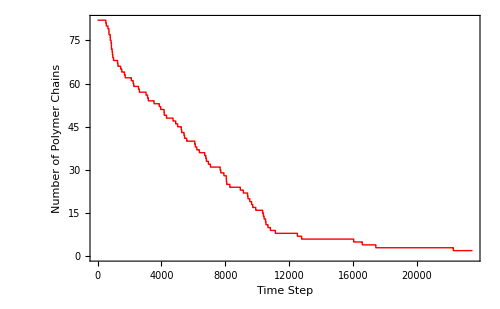

```mathematica
ListLinePlot[Length/@cleanPositions,Frame->True,FrameLabel->{"Time Step","Number of Polymer Chains"},ImageSize->500,LabelStyle->Directive[Black,Thick,18],PlotStyle->Directive[Red,Thick]]
```

```mathematica
lines=Thread[{Count[True]/@Map[polymerLoopQ,cleanPositions,{2}],Length/@cleanPositions}];
```

```mathematica
events=Most[Accumulate[Prepend[Length/@Split[lines],1]]];
eventFrames=Table[Graphics[{
chainGraphic/@cleanPositions[[i]]
},PlotRange->{{-boxSize,boxSize}/2,{-boxSize,boxSize}/2},ImageSize->350],{i,events}];
```

```mathematica
Multicolumn[eventFrames[[;;-3]],4,Appearance->"Horizontal"]
```

```mathematica
Manipulate[noSelfLoopFrames[[a]],{a,7000,7249,1}]
```

```mathematica
noSelfLoopFrames=Table[Graphics[{
chainGraphic/@cleanPositions[[i]]
},PlotRange->{{-boxSize,boxSize}/2,{-boxSize,boxSize}/2},ImageSize->350],{i,15000}];
```

```mathematica
Export["step-growth-polymerization__no-self-loops__82-dimers__15000-frames.mx",Take[cleanPositions,15000]]
```

step-growth-polymerization__no-self-loops__82-dimers__15000-frames.mx

```mathematica
Export["step-growth-polymerization__no-self-loops__82-dimers__reptation.gif",noSelfLoopFrames[[7000;;7249]]]
```

step-growth-polymerization__no-self-loops__82-dimers__reptation.gif

```mathematica
Export["step-growth-polymerization__no-self-loops__82-dimers__events.gif",eventFrames[[;;-3]]]
```

step-growth-polymerization__no-self-loops__82-dimers__events.gif

```mathematica
noSelfLoopFrames[[a]]
```

```mathematica
Export["step-growth-polymerization__no-self-loops__82-dimers__15000-frames.gif",noSelfLoopFrames]
```

$Aborted

```mathematica
SeedRandom[1];
boxSize=55;
listOfPositions=randomPackingDimerConfiguration[boxSize,3/2];

positions=QuietEcho[nestListWithMonitor[moveAllChains[#,0.1,0.1,boxSize,False]&,listOfPositions,15000]];
```

```mathematica
cleanPositions2=DeleteDuplicates[positions];
```

```mathematica
lines2=Thread[{Count[True]/@Map[polymerLoopQ,cleanPositions2,{2}],Length/@cleanPositions2}];
events2=Most[Accumulate[Prepend[Length/@Split[lines2],1]]];
eventFrames2=Table[Graphics[{
chainGraphic/@cleanPositions2[[i]]
},PlotRange->{{-boxSize,boxSize}/2,{-boxSize,boxSize}/2},ImageSize->350],{i,events2}];
```

```mathematica
Export["step-growth-polymerization__self-loops__82-dimers__events.gif",eventFrames2]
```

step-growth-polymerization__self-loops__82-dimers__events.gif

```mathematica
positions2=QuietEcho[nestListWithMonitor[moveAllChains[#,0.1,0.1,boxSize,False]&,Last[positions],15000]];
```

$Aborted

```mathematica
Graphics[{
chainGraphic/@positions[[-1000]]
},PlotRange->{{-boxSize,boxSize}/2,{-boxSize,boxSize}/2},ImageSize->350]
```

```mathematica
noSelfLoopFrames=Table[Graphics[{
chainGraphic/@cleanPositions[[i]]
},PlotRange->{{-boxSize,boxSize}/2,{-boxSize,boxSize}/2},ImageSize->350],{i,15000}]
```

```mathematica
Export["step-growth-polymerization__self-loops__52-dimers.mx",cleanPositions]
```

step-growth-polymerization__self-loops__52-dimers.mx

Movie Version w/o self-loops

```mathematica
SeedRandom[1];
boxSize=55;
listOfPositions=randomPackingDimerConfiguration[boxSize,2];

positions=QuietEcho[nestListWithMonitor[moveAllChains[#,0.05,0.1,boxSize,True]&,listOfPositions,250000]];
```

```mathematica
SeedRandom[15];
listOfPositions=Table[collisionFreeCorrelatedPolymerChain2D[RandomInteger[{8,12}],0.3,RandomReal[{-8,8},2]],4];
bbs=axesAlignedBoundingBoxes/@listOfPositions;
cols=RandomColor[4];

reptationPositions=DeleteDuplicates[QuietEcho[nestListWithMonitor[moveAllChains[#,0.1,0.1,1000,True]&,listOfPositions,250]]];
```

```mathematica
reptationFrames=Table[Graphics[Map[chainGraphic,DeleteDuplicates[reptationPositions][[a]]]],{a,200}];
```

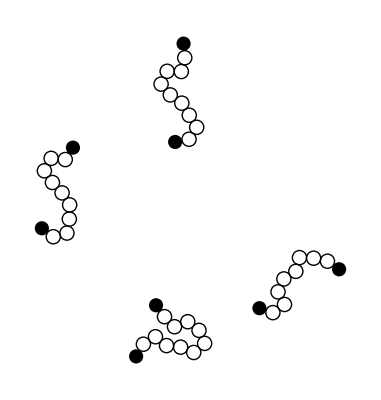

```mathematica
reptationFrames[[2]]
```

```mathematica
DeleteDuplicates[reptationPositions]//Length
```

251

```mathematica
Export["step-growth-polymerization__4-chains__reptation.gif",reptationFrames]
```

step-growth-polymerization__4-chains__reptation.gif

```mathematica
chainGraphicWithBBs[]
```

```mathematica
Manipulate[Graphics[MapThread[chainGraphicBBs,{reptationPositions[[a]],cols}]],{a,1,250,1}]
```

```mathematica
makeReptationFrame[]
```

## Initialization Functions

### Visualization

```mathematica
chainGraphicBBs[positions_,col_]:=With[{bb=axesAlignedBoundingBoxes[positions]}, {
{Opacity[0.25],col,Rectangle@@Transpose[bb]},
{FaceForm[None],EdgeForm[col//Darker],Disk[#,1/2]&/@positions[[2;;-2]]},
{FaceForm[col//Darker],EdgeForm[Black],Disk[#,1/2]&/@positions[[{1,-1}]]}
}
]
```

```mathematica
chainGraphic[positions_,bb_,col_:RandomColor[]]:= {
{Opacity[0.25],col,Rectangle@@Transpose[bb]},
{FaceForm[None],EdgeForm[col//Darker],Disk[#,1/2]&/@positions[[2;;-2]]},
{FaceForm[col//Darker],EdgeForm[Black],Disk[#,1/2]&/@positions[[{1,-1}]]}
}
```

```mathematica
polymerLoopQ[particles_]:=Norm[particles[[1]]-particles[[-1]]]//Chop//PossibleZeroQ
```

```mathematica
chainGraphic[positions_]:= {
{Circle[#,1/2]&/@positions[[2;;-2]]},
{Disk[#,1/2]&/@positions[[{1,-1}]]}
}

chainGraphic[positions_?polymerLoopQ]:={Circle[#,1/2]&/@positions}
```

```mathematica
nestListWithMonitor[f_,init_,n_]:=Module[{it=0},
PrintTemporary[ProgressIndicator[Dynamic[it/n]]];
NestList[(it++;f[#])&,init,n]]
```

### Correlated Polymer Microstructures

```mathematica
collisionQ[nf_NearestFunction,bondLength_:1][candidatePt_]:=First[nf[candidatePt]]<bondLength

angularRange[correlation_]:={-1,1}(1-correlation)2π/3

addCorrelatedParticleToChain[correlation_][chainSoFar_]:=Block[{
nf=Nearest[chainSoFar->"Distance"],
angleRange=angularRange[correlation],
lastAngle=ArcTan@@(chainSoFar[[-1]]-chainSoFar[[-2]]),
newAngle,candidate,collision
},

newAngle=RandomReal[angleRange]+lastAngle;
candidate=Last[chainSoFar]+AngleVector[newAngle];

collision=collisionQ[nf][candidate];
If[collision,chainSoFar,Append[chainSoFar,candidate]]

]

Clear[collisionFreeCorrelatedPolymerChain2D]
collisionFreeCorrelatedPolymerChain2D[numberUnits_,correlation_,origin_:{0,0},maxAttempts_:100]:=With[{start=Join[{origin},{AngleVector[origin,RandomReal[angularRange[correlation]]]}]},
NestWhile[addCorrelatedParticleToChain[correlation],start,Length[#]<numberUnits&,1,maxAttempts]
]

randomDimer[origin_]:=Join[{origin},{AngleVector[origin,RandomReal[2π]]}]

hexagonalDimerConfiguration[size_,linearSpacingFactor_:1]:=Block[{
hexagonalLatticeVectors={{1,0},{1/2,Sqrt[3]/2}},
latticeCoords=Tuples[linearSpacingFactor Range[-size,size,3],2],sites,cleanSize=size-3},
sites=Select[latticeCoords.hexagonalLatticeVectors,cleanSize/2>#[[1]]>-cleanSize/2&&cleanSize/2>#[[2]]>-cleanSize/2&];
randomDimer/@sites
]

randomPackingDimerConfiguration[size_,linearSpacingFactor_:1]:=Block[{
proc=HardcorePointProcess[1,3 linearSpacingFactor,2],sites,cleanSize=size-3},
sites=RandomPointConfiguration[proc,Rectangle[{-cleanSize/2,-cleanSize/2},{cleanSize/2,cleanSize/2}]]["Points"];
randomDimer/@sites
]
```

### Single Chain Reptation

```mathematica
precompute[positions_,perturbedIndex_,s_,ν_, θ_]:= Block[
{
dp = Differences[positions],
betaList,
diffs,
reducedAngles
},
betaList =ArcTan@@@ Join[-dp[[1;;perturbedIndex-1]],dp[[perturbedIndex;;-1]]] ;
reducedAngles=θ +2 ArcCot[ⅇ^(-s+s ν)Cot[(betaList-θ)/2]];
reducedAngles=Insert[reducedAngles,θ,perturbedIndex];
Transpose@{Cos[reducedAngles],Sin[reducedAngles]}]

displacementsBase[perturbedIndex_,positionList_,s_,ν_,θ_]:= 
Block[{newPositions,betaList,Δ  },
Δ=precompute[positionList,perturbedIndex,s,ν,θ];

newPositions[perturbedIndex] =positionList[[perturbedIndex]]+s AngleVector[θ];

newPositions[index_] := newPositions[index]=
Module[{nextIndex=index-Sign[index-perturbedIndex]},
newPositions[nextIndex] + Δ[[index]]
];

newPositions/@Range[Length[Δ]]
]
```

```mathematica
displacements[perturbedIndex_,positionList_,s_,ν_,θ_]:= 
displacementsBase[perturbedIndex,positionList,s,ν,θ]

displacements[perturbedIndex_,positionList_?polymerLoopQ,s_,ν_,θ_]:=Block[{firstStep,angle,disp,squaredNorm,minimumS,newPositions},

firstStep=displacementsBase[perturbedIndex,positionList,s,ν,θ];
angle=ArcTan@@(firstStep[[1]]-firstStep[[-1]]);

newPositions=displacementsBase[Length[positionList],firstStep,ds,ν,angle];
disp=Subtract@@newPositions[[{1,-1}]];
squaredNorm=disp.disp;

enforceClosedLoopEnd[newPositions/.First[Quiet[FindRoot[squaredNorm,{ds,s,0.,1.},AccuracyGoal->4,PrecisionGoal->4]]]]
]

enforceClosedLoopEnd[positionList_]:=ReplacePart[positionList,Length[positionList]->positionList[[1]]]
```

```mathematica
collisionFreeQ[positions_]:=With[{nf=Nearest[positions]},Total[Length[nf[#,{All,1.-10^-6}]]&/@positions]<=Length[positions]]

collisionFreeLoopQ[positions_?polymerLoopQ]:=collisionFreeQ[Most[positions]]

endPointsCollisionQ[positions_]:=With[{dr=positions[[1]]-positions[[-1]]},dr.dr<1]

mergeEndPointsSingle[positions_]:=Append[positions,First[positions]]

moveSingleChain[positions_,ds_,stickiness_,size_,forbidLoops_:False]:= 
Block[{newPositions,cleanSize=size-1},

newPositions= displacements[RandomInteger[{1,Length[positions]}],positions,ds,stickiness,RandomReal[2π]];

If[Max[Abs[MinMax[newPositions]]]>cleanSize/2,Return[positions]];

If[forbidLoops,
If[collisionFreeQ[newPositions],newPositions,positions],

If[polymerLoopQ[newPositions],If[collisionFreeLoopQ[newPositions],Return[newPositions],Return[positions]]];
If[collisionFreeQ[newPositions],Return[newPositions]];

If[endPointsCollisionQ[newPositions],
mergeEndPointsSingle[newPositions]
,positions]
]

]
```

### Multiple Chain Reptation

```mathematica
axesAlignedBoundingBoxes[positions_]:={{-1/2,1/2},{-1/2,1/2}}+MinMax/@Transpose[positions]

horizontalAxesAlignedIntersection[{{xMinA_,xMaxA_},{yMinA_,yMaxA_}},{{xMinB_,xMaxB_},{yMinB_,yMaxB_}}]:=(xMaxA>xMinB&&xMinA<xMaxB)
verticalAxesAlignedIntersection[{{xMinA_,xMaxA_},{yMinA_,yMaxA_}},{{xMinB_,xMaxB_},{yMinB_,yMaxB_}}]:=(yMaxA>yMinB&&yMinA<yMaxB)

connectivityMatrixIndexHorizontal[bbs_,{i_,j_}]:=horizontalAxesAlignedIntersection[bbs[[i]],bbs[[j]]]
connectivityMatrixIndexVertical[bbs_,{i_,j_}]:=verticalAxesAlignedIntersection[bbs[[i]],bbs[[j]]]//Boole

connectivityMatrix[bbs_]:=Block[{s=Subsets[Range[Length[bbs]],{2}],l=Length[bbs],pruneHorizontally},
pruneHorizontally=Select[s,connectivityMatrixIndexHorizontal[bbs,#]&];
SparseArray[pruneHorizontally->(connectivityMatrixIndexVertical[bbs,#]&/@pruneHorizontally),{l,l}]
]

returnPointsInOverlap[{positionsA_,{{xMinA_,xMaxA_},{yMinA_,yMaxA_}}},{positionsB_,{{xMinB_,xMaxB_},{yMinB_,yMaxB_}}}]:=With[
{
xMin=Max[xMinA,xMinB]-1/2,yMin=Max[yMinA,yMinB]-1/2,
xMax=Min[xMaxA,xMaxB]+1/2,yMax=Min[yMaxA,yMaxB]+1/2
},
Table[Select[Thread[{pos,Range[Length[pos]]}],xMax>#[[1,1]]>xMin&&yMax>#[[1,2]]>yMin&],{pos,{positionsA,positionsB}}]
]

returnAllCollisions[posA_,posB_]:=Block[{nf,sorted,
posShortcoords,posShortIndices,
posLongcoords,posLongIndices,
cols},

sorted=SortBy[{posA,posB},Length];
posShortcoords=sorted[[1,All,1]];posShortIndices=sorted[[1,All,2]];
posLongcoords=sorted[[2,All,1]];posLongIndices=sorted[[2,All,2]];

nf=Nearest[posLongcoords->{"Index","Distance"}];
cols=Select[Prepend[First[nf[posShortcoords[[#]]]],#]&/@Range[Length[posShortcoords]],#[[3]]<1&];

{posLongIndices[[#2]],posShortIndices[[#1]],#3}&@@@cols

]

pairwiseChainCollisions[{listOfPositions_,bbs_},{i_,j_}]:=Block[{
posA=listOfPositions[[i]],bbA=bbs[[i]],
posB=listOfPositions[[j]],bbB=bbs[[j]]
},

{posA,posB}=returnPointsInOverlap[{posA,bbA},{posB,bbB}];
If[Length[posA]==0||Length[posB]==0,{},returnAllCollisions[posA,posB]]
]
```

```mathematica
compareEndPoints[listOfPositions_,{i_,j_}]:=
Block[{
endsI=listOfPositions[[i,{1,-1}]],
endsJ=listOfPositions[[j,{1,-1}]],
vecs},

vecs=Tuples[{endsI,endsJ}];
Thread[SquaredEuclideanDistance@@@vecs<1]
]

mergeEndPoints[listOfPositions_,{i_,j_},pairwiseEndPointChecks_]:=With[{posI=listOfPositions[[i]],posJ=listOfPositions[[j]]},
Switch[pairwiseEndPointChecks,
{True,_,_,_},ReplacePart[listOfPositions,checkProposedMerger[{i,j},{Reverse[posI],posJ}]],
{False,True,_,_},ReplacePart[listOfPositions,checkProposedMerger[{i,j},{posJ,posI}]],
{False,False,True,_},ReplacePart[listOfPositions,checkProposedMerger[{i,j},{posI,posJ}]],
{False,False,False,True},ReplacePart[listOfPositions,checkProposedMerger[{i,j},{posI,Reverse[posJ]}]],
_,listOfPositions
]
]

collisionFreeFurtherQ[positions_]:=With[{nf=Nearest[positions->All],l=Length[positions]},
Length[Join@@Table[Select[nf[positions[[i]],{All,1}],Abs[#Index-i]>1&],{i,l}]]==0]

checkProposedMerger[{i_,j_},{posI_,posJ_}]:=
With[{proposal=Join[posI,posJ]},
If[collisionFreeFurtherQ[proposal],{{i},{j}}->proposal,Echo["Intersecting Merger"];{}]
]
```

```mathematica
checkForCollisions[{listOfPositions_,oldListOfPositions_},forbidLoops_:False]:=Catch[
Block[{
listOfPos=listOfPositions,
bbs=axesAlignedBoundingBoxes/@listOfPositions,
mij,nonzero,collisions,collisionIndices,endpointChecks,lengths},

mij=connectivityMatrix[bbs];
If[mij["ExplicitLength"]==0,Echo["No Bounding Box Collisions"];Return[listOfPos]];

nonzero=mij["NonzeroPositions"];
collisions=pairwiseChainCollisions[{listOfPos,bbs},#]&/@nonzero;
If[Length[Join@@collisions]==0,Echo["No Collisions"];Return[listOfPos]];

lengths=Sort[Length/@Extract[listOfPos,List/@#]]&/@nonzero;

If[Not[forbidLoops],
Do[
If[
Length[collisions[[a]]]>0&&
Or@@polymerLoopQ/@Extract[listOfPos,List/@nonzero[[a]]],
Echo["Collision with loop"];Throw[oldListOfPositions]],{a,Length[collisions]}]
];

Do[
If[
Length[collisions[[a]]]>0&&
(1<collisions[[a,j,1]]<lengths[[a,1]]||
1<collisions[[a,j,2]]<lengths[[a,2]]),
Echo["No-terminating collisions"];Throw[oldListOfPositions]],{a,Length[collisions]},{j,Length[collisions[[a]]]}];

collisionIndices= Extract[nonzero,Position[collisions,Except[{}],1,Heads->False]];
endpointChecks=compareEndPoints[listOfPos,#]&/@collisionIndices;
If[Nor@@Flatten[endpointChecks],Echo["No Mergers"];Return[oldListOfPositions]];

Do[
listOfPos=mergeEndPoints[listOfPos,collisionIndices[[a]],endpointChecks[[a]]],
{a,Length[collisionIndices]}
];

DeleteDuplicates[listOfPos]
]
]

moveAllChains[listOfPositions_,ds_,stickiness_,size_,forbidLoops_:False]:= Block[{listOfPos=listOfPositions},
listOfPos=moveSingleChain[#,ds,stickiness,size,forbidLoops]&/@listOfPos;
checkForCollisions[{listOfPos,listOfPositions},forbidLoops]
]
```